Solving the Poisson-Fermi-Dirac equation in LLZO
Michael W Swift and James W Swift

Accompanying “Modeling the electrical double layer at solid-state electrochemical interfaces” by Michael W Swift, James W Swift, and Yue Qi

We consider the system

```mathematica
v' = a(f)
f'==v
a(f) = 1/(B ⅇ^-f+1)-1/(B ⅇ^f+1)
```

The asymptotic behavior of f is represented by the fixed point at (0,0) in this system of equations.  Any solution on the stable manifold of this fixed point will have the correct asymptotic behavior.  To do so, we will find a point some small distance ϵ from the fixed point in the stable eigenspace of the fixed point, then evolve backwards in time to find a point that matches the initial condition for f.  We set x=0 at that point, and this gives us the solution.

The Jacobian of this system at the critical point (0,0) is

```mathematica
J = ({{(∂v)/(∂f), (∂v)/(∂v)}, {(∂a)/(∂f), (∂a)/(∂v)}})=({{0, 1}, {(2B)/(1+B)^2, 0}})
```

The stable eigenspace is spanned by the eigenvector

```mathematica
V=({{(B+1)/B}, {-√(2/B)}})  , J V = ({{-√(2/B)}, {2/(B+1)}})  = (-√(2B))/(B+1)V
```

We therefore take V*ϵ as the starting point for some small ϵ.  Save V as eigen below:

```mathematica
eqn=f''[x]==1/(B*ⅇ^(-f[x])+1)-1/(B*ⅇ^f[x]+1);
```

```mathematica
a[f_,B_]:=1/(B*ⅇ^-f+1)-1/(B*ⅇ^f+1);
```

```mathematica
eigen={(B+1)/B,-(√2)/(√B)};
```

```mathematica
asymptoticSolution[eqn_,eigen_,BIn_,f0_]:=Module[{eps,xEvec,xMax,unstableManifold,xSol},
eps = 1/1000;
xEvec = 10^11; (* large:  This is the value of x where we impose that the solution is close to the fixed point at the origin, in the direction of the stable eigenvector *)
xMax =xEvec + 10; (* xMax ≥ xEvec.  This can be used so see the solution divierge to infinity or -infinity *)
unstableManifold= Part[NDSolve[{eqn/.B->BIn,
 f[xEvec]== eps*eigen[[1]]/.B->BIn, f'[xEvec]==eps*eigen[[2]]/.B->BIn},f, {x,0,xMax}], 1];
(* Solve backwards in time starting from eps*eigen *)  
(* Take the first and only solution *)
xSol=Part[FindRoot[f[x0]==f0/.unstableManifold,{x0,3.5*10^9},AccuracyGoal->5,PrecisionGoal->5],1];
(* Find x0 corresponding to f0 *)
{unstableManifold,x0/.xSol,xEvec}
(* Return replacement rule for the solution, x0, and xEvec *)];
```

```mathematica
U[f_, B_] :=  -Log[ (Exp[f] + B)/(1+B)] +-Log[ (Exp[-f] + B)/(1+B)];
p0[f0_,B_]:=Sqrt[-2*U[f0,B]];
fa[x_,f0_,B_]:=Log[1 + (Tan[(p0[f0,B]-x)/Sqrt[2 B]+ ArcTan[Sqrt[Exp[f0 - 1/2p0[f0,B]^2]-1]]])^2];
f0Prime[f_,B_]:=-Sqrt[-2*U[f, B ] ];
fExp[f0_,B_,x_]:=fa[Sqrt[B/2],f0,B]*Exp[-x/Sqrt[B/2]+1];

(* New version *)
cVal = 7.39;
fExp[f0_,B_,x_]:=Exp[-(x-cVal)/Sqrt[B/2]];
```

```mathematica
(* Physical constants *)
e=Quantity[1,"electron charge"];
k=Quantity[1,"BoltzmannConstant"];
T=Quantity[300,"K"];
ϵ0=Quantity[1,"ϵ0"];
```

```mathematica
(* Materials properties: input *)
materialName="LLZO";
ϵr=50; (* Dielectric constant 
https://doi.org/10.1021/acs.inorgchem.5b01895 Figure S2*)
ϕ0=Quantity[-1.6216363422810787,"Volts"]; (* Potential offset with electrode*)(*NSites= Quantity[0.000454798699321109, "Angstroms^-3"]; *)
NSites=UnitConvert[(24+48)/(Quantity[13.0035, "Angstroms"]^3), "cm^-3"]
(*NSites=UnitConvert[32 / Quantity[8.116767673775174, "Angstroms"]^3,"cm^-3"]; *)(* Density of defect sites *)
Eform=Quantity[0.014390739738404434,"eV"]; (* Defect formation energy at charge neutrality *)
α=0.1;(* Saturation factor *)
```

3.27455×10^22 /cm^3

```mathematica
(* Derived quantities *)
ftoV = QuantityMagnitude[UnitConvert[k*T/e,"Volts"]];
BIn=SetPrecision[α*Exp[Eform/(k*T)],100];
λ=SetPrecision[QuantityMagnitude[UnitConvert[√((ϵr ϵ0 k T)/(α*NSites e^2)),"Angstroms"]],100];
f0=SetPrecision[-(e ϕ0)/(k T),100];
ϕ0mag=QuantityMagnitude[ϕ0];

(* Solve it *)
{sol,x0,xEvec}=asymptoticSolution[eqn,eigen,BIn,f0];

(* Dimensionless parts *)
fp0=f0Prime[f0,BIn];
fp0Numerical=f'[x0]/.sol;
quadraticPiece[x_]:=f0+fp0*x+1/2x^2;
logarithmicPiece[x_]:=fa[x,f0,BIn];
exponentialPiece[x_]:=fExp[f0,BIn,x];

(* Return dimensions *)
ϕ[x_]:=-ϕ0mag-ftoV*f[x/λ+x0]/.sol;
ϕ1[x_]:=-ϕ0mag-ftoV*quadraticPiece[x/λ];

Print[materialName]

Print["For tab:PFD_params"]
Print[StringForm["f0 = ``, f'0 = `` (Numerical solution has f'0 = ``), λ = `` Å, B = ``",NumberForm[f0,4],NumberForm[fp0,4],NumberForm[fp0Numerical,4] ,NumberForm[λ,4], NumberForm[BIn,4] ]]
Print[];

ξ1=-fp0;x1=ξ1*λ;
ξ2=Sqrt[BIn]/2;x2=ξ2*λ;

surfaceCharge=UnitConvert[Sqrt[α*NSites*k*T*ϵ0/ϵr]*fp0, "electron charge/nm^2"];

Print["For tab:crossover_thicknesses"]
Print[StringForm["x1 = `` Å, ϕ(x1) = `` V, ϕ(∞) = `` V, σ Li = ``",
NumberForm[x1,3], NumberForm[ϕ[x1],3],NumberForm[-ϕ0mag,3],NumberForm[surfaceCharge,3]]]

capacitance=UnitConvert[surfaceCharge/ϕ0,"microFarad / cm^2"]

Print["For tab:crossover_thicknesses"]
Print[StringForm["x1 = `` Å, ϕ(x1) = `` V, x2 = `` Å, ϕ(x2) = `` V, ϕ(∞) = `` V, σ Li = ``",
NumberForm[x1,3], NumberForm[ϕ[x1],3],NumberForm[x2,3], NumberForm[ϕ[x2],3],NumberForm[-ϕ0mag,3],NumberForm[surfaceCharge,3]]]
Print[];
```

LLZO

For tab:PFD_params

f0 = 62.73, f'0 = -11.01 (Numerical solution has f'0 = -11.01), λ = 1.477 Å, B = 0.1745

For tab:crossover_thicknesses

x1 = 16.3 Å, ϕ(x1) = 1.58 V, ϕ(∞) = 1.62 V, σ Li = -0.107

1.05264 µF/cm^2

For tab:crossover_thicknesses

x1 = 16.3 Å, ϕ(x1) = 1.58 V, x2 = 0.308 Å, ϕ(x2) = 0.0589 V, ϕ(∞) = 1.62 V, σ Li = -0.107

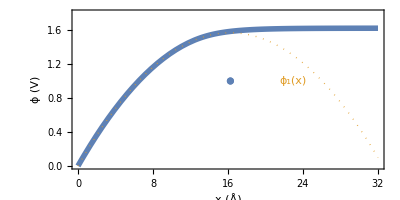

-Graphics-

```mathematica
xMax=(xEvec-x0)*λ;Show[Plot[{ϕ[x],ϕ1[x],ϕ0},{x,0.001,xMax},FrameStyle->Directive[14,Black],AspectRatio->1/2,PlotRange->{{0,xMax},{0,1.8}},FrameLabel->{"x (Å)","ϕ (V)"},PlotStyle->{Thickness[0.01],{Thick,Dotted},{Thin,Black}},Frame->True, Epilog->{
Text[Style["ϕ_1(x)",{Medium,ColorData[97,2]}], {23,1.0}]}],
ListPlot[{{x1,1.0}}]
]


conc[x_]:=α*QuantityMagnitude[UnitConvert[NSites,"cm^-3"]]*a[(f[x/λ+x0])/.sol,BIn];

Plot[conc[x],{x,0,xMax},Frame->True,PlotRange->{{0,xMax},All},FrameStyle->Directive[14,Black],AspectRatio->1/3,FrameLabel->{"x (Å)","c^+ (cm^-3)"}]
```

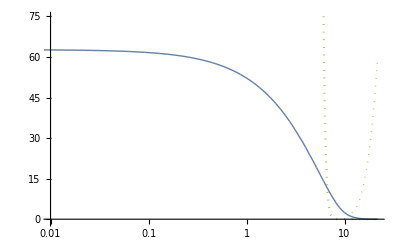

```mathematica
LogLinearPlot[{f[x+x0]/.sol,quadraticPiece[x],exponentialPiece[x]},{x,0.0001,xEvec-x0},FrameStyle->Directive[14,Black],PlotRange->{{0.01,xEvec-x0},{-1,75}},FrameLabel->{ξ,f},PlotStyle->{Thick,{Thick,Dotted},Dotted,Dotted}]
```